```mathematica
H={{-6,-6,-7,0,7,6,6,-3,-3,0,0,-6},{-7,2,1,8,1,2,-7,-7,-2,-2,-7,-7}};
```

```mathematica
MatrixForm[H]
```

(-6 | -6 | -7 | 0 | 7 | 6 | 6 | -3 | -3 | 0 | 0 | -6
-7 | 2 | 1 | 8 | 1 | 2 | -7 | -7 | -2 | -2 | -7 | -7)

```mathematica
DrawHouse[A_]:=ListLinePlot[Transpose[A.H],Axes->False,AspectRatio->1,Filling->False]





AList = {IdentityMatrix[2],{{Cos[35 Degree],-Sin[35 Degree]},{Sin[35 Degree],Cos[35 Degree]}},{{0,1},{1,0}},{{0.7,0.3},{0.3,0.7}},{{0.7,0.2},{-0.3,0.9}},{{0,1.1},{0.1,0.3}}};
```

```mathematica
h
```

h

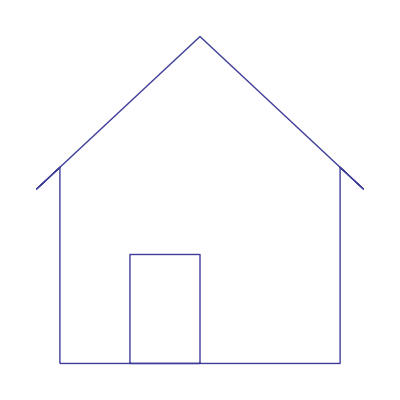
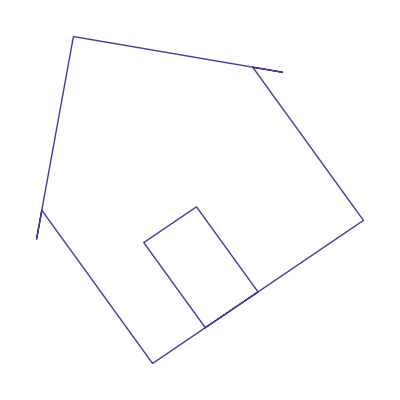
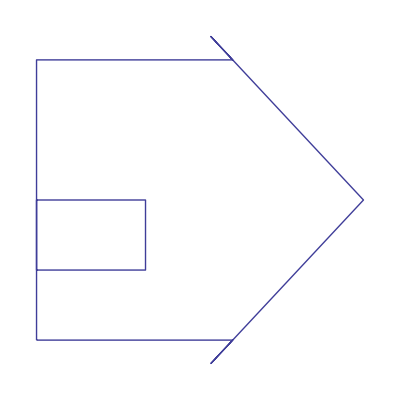
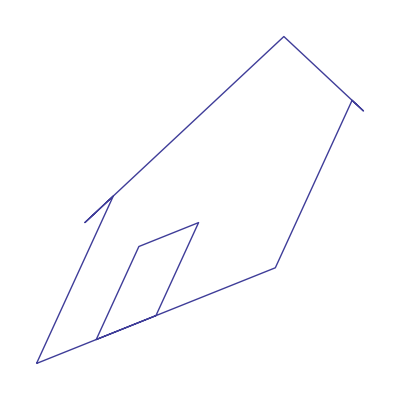
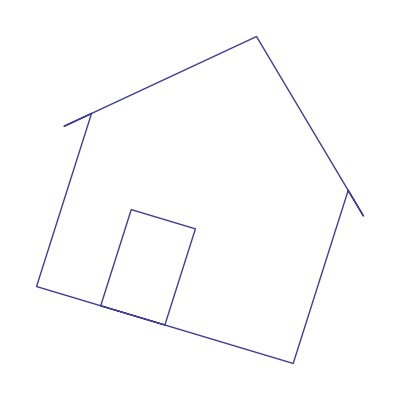
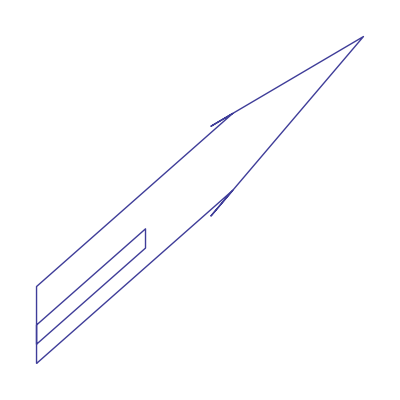

```mathematica
DrawHouse /@ AList
```

```mathematica
Animate[   DrawHouse[ {{Cos[t],-Sin[t]},{Sin[t],Cos[t]}}],{t,0,4*Pi}]
```

```mathematica
Animate[ DrawHouse[ {{1,t},{0,1}}],{t,0,3}]
```

```mathematica
Textbook=Import["http://mybookofrai.typepad.com/my_weblog/images/turkey.jpg"]
```

-Graphics-

-Graphics-

```mathematica
Textbook[[2]]
```

ImageSize→{400,369}

```mathematica
Textbook[[2]]
```

ImageSize→{400,369}

```mathematica
Animate[Graphics[Rotate[Textbook[[1]],a],PlotRange->{{-50,400},{-50,400}},AspectRatio->1,Axes->True],{a,0,360 Degree}]
```

```mathematica
TransformTextbook[A_]:=Graphics[GeometricTransformation[Textbook[[1]],A],PlotRange->{{-300,500},{-300,500}},AspectRatio->1]
```

```mathematica
TransformTextbook  /@ AList
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Animate[ TransformTextbook[  {{Cos[t],-Sin[t]},{Sin[t],Cos[t]}}.{{1,t},{0,1}}], {t,0,120 Degree}]
```

```mathematica
li
```

li

```mathematica
"
```